{{y→InterpolatingFunction[…]}}

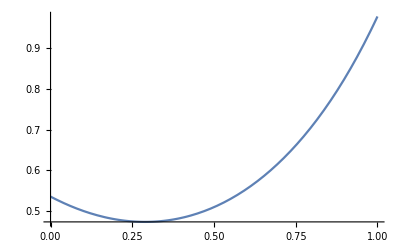

```mathematica
S1=NDSolve[{y''[x]+x/(1.53 + x^2)   y'[x]- (1+Sin[x])/(√(1.38^2+ x^2))y[x]== Exp[1.38*x^2],y[0]-1.1*y'[0] == 1, 3.75*y[1]+0.6*y'[1]==4.7},y,{x,0,1}]
Plot[y[x]/.S1,{x,0,1}]
```